```mathematica
ClearAll[newdata,species,col,AH,BH,CH,Tred,H,x]
```

```mathematica
Manipulate[
Module[{newdata,species,col,AH,BH,CH,Tred,H,x},
newdata[data_]:=Delete[data,Position[{helium,hydrogen,nitrogen,oxygen,carbonmonoxide,carbondioxide,methane,ethane},False]];
species=newdata@{"helium","hydrogen","nitrogen","oxygen","CO",Subscript["CO",2],"methane","ethane"};

col=newdata[{Thick,Hue[#]}&/@Range[0,1,0.1]];

AH={-3.52839,-4.73284,-9.67578,-9.44833,-10.52862,-8.55445,-10.44708,-19.67563};
BH={7.12983,6.08954,4.72162,4.43822,5.13259,4.01195,4.66491,4.51222};
CH={4.4777,6.06066,11.70585,11.42005,12.01421,9.52345,12.12986,20.62567};

Tred=(temp+273)/647;
H=(P/10)*Exp[AH/Tred+(BH*(1-Tred)^0.355)/Tred+CH*Tred^-0.41*ⅇ^(1-Tred)];
x=newdata[1/H];

Show[Switch[npr,
True,
BarChart[x/.temp->T,ChartStyle->Flatten@Delete[col,Position[col,Thick]],ChartLabels->Placed[Rotate[Style[#,17],45 °]&/@species,Below],FrameTicks->{{True,True},{None,None}},FrameLabel->{None,Style["mole  fraction  gas  dissolved  ",17]},PlotRangePadding->{None,{None,Scaled[0.02]}}],
False,
Plot[x,{temp,0,250},PlotStyle->col,FrameLabel->{Style["temperature (°C)",17],Style["mole  fraction  gas  dissolved  ",17]},PlotRangePadding->{None,Scaled[0.02]},PlotRangeClipping->False,PlotRange->All(*,Epilog->
Table[Mouseover[{Transparent,Line[Table[{temp,x[[i]]},{temp,0,250}]]},Text[Style[species[[i]],17,col[[i]],Background->White],Dynamic@MousePosition["Graphics"],{0,-1.5}]],{i,1,Length[x]}]*)]
],
Axes->False,Frame->True,LabelStyle->{14,Black},ImageSize->{600,370},AspectRatio->Full,ImagePadding->{{70,35},{65,15}},
PlotRange->All];
x
],
Grid[{
{Style["select species to plot:",Bold],
Control[{{helium,True,"helium"},{True,False}}],
Control[{{hydrogen,True,"hydrogen"},{True,False}}],
Control[{{nitrogen,True,"nitrogen"},{True,False}}],
Control[{{oxygen,True,"oxygen"},{True,False}}]},
{Spacer[1],
Control[{{carbonmonoxide,True,"CO"},{True,False}}],
Control[{{carbondioxide,True,Subscript["CO",2]},{True,False}}],
Control[{{methane,True,"methane"},{True,False}}],
Control[{{ethane,True,"ethane"},{True,False}}]}
},Alignment->Right],
Spacer[1],
Grid[{{
Control[{{npr,True,"set temperature"},{True,False}}],Spacer[5],
Control[{{P,5,"partial pressure (bar)"},1,5,0.1,Appearance->"Labeled",ImageSize->Small}],
PaneSelector[{True->Control[{{T,0,"temperature (°C)"},0,250,1,Appearance->"Labeled",ImageSize->Small}]},Dynamic@npr]
}}]
]
```

```mathematica
{{274,343},{273,353},{273,353},{275,323},{287
```

```mathematica
Module[{data},
data={{"helium",273,348},{"hydrogen",287,346},{"nitrogen",273,350},{"oxygen",273,333},{"CO",273,353},{"CO_2",273,353},{"methane",273,523},{"ethane",275,323}};
N@{Sum[data[[i,2]],{i,1,Length[data]}]/Length[data],
Sum[data[[i,3]],{i,1,Length[data]}]/Length[data]}-273
]
```

{2.,93.125}

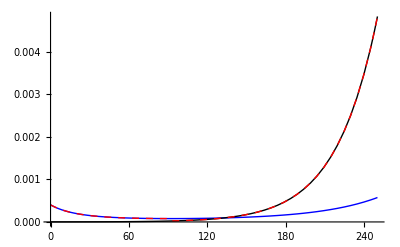

```mathematica
Module[{e1,e2,e3},
e1=5*ⅇ^(-250.812+12695.6/(273+temp))*(273+temp)^34.7413;
e2=2*ⅇ^(12730.13261/(273+temp)-(2919.40634*(1+1/647*(-273-temp))^0.355)/(273+temp)-(293.00755606051206*ⅇ^(1+1/647*(-273-temp)))/(273+temp)^0.41);
e3=Piecewise[{{e1,0≤temp≤93},{e2,93<temp≤250}}];

Plot[{e1,e2,e3},{temp,0,250},PlotStyle->{{Thick,Blue},{Thick,Black},{Thick,Dashed,Red}},PlotRange->All]
]
```

```mathematica
323-273
```

50

```mathematica
{{273,348},{287,346},{273,350},{273,333},{273,353},{273,353},{273,523},{275,323}}-273
```

{{0,75},{14,73},{0,77},{0,60},{0,80},{0,80},{0,250},{2,50}}

```mathematica
Tmax=Table[{{"helium",273,348},{"hydrogen",287,346},{"nitrogen",273,350},{"oxygen",273,333},{"CO",273,353},{"CO_2",273,353},{"methane",273,523},{"ethane",275,323}}[[i,3]],{i,1,8}]-273
```

{75,73,77,60,80,80,250,50}

```mathematica
Manipulate[
Module[{newdata,species,AH,BH,CH,DH},
newdata[data_]:=Delete[data,Position[{acetylene,carbondioxide,carbonmonoxide,ethane,ethylene,helium,hydrogen,methane,nitrogen,oxygen},False]];
species=newdata@{"acetylene",Subscript["CO",2],"CO","ethane","ethylene","helium","hydrogen","methane", "nitrogen","oxygen" };

AH={-156.51,-159.854,-171.764,-250.812,-153.027,-105.9768,-125.939,-338.217,-181.587,-171.2542};
BH={8160.2,8741.68,8296.9,12695.6,7965.2,4259.62,5528.45,13282.1,8632.12,8319.24};
CH={21.403,21.6694,23.3376,34.7413,20.5248,14.0094,16.8893,51.9144,24.7981,23.24323};
DH={0,-1.10261*^-3,0,0,0,0,0,-0.0425831,0,0};

Column[{newdata@AH,newdata@BH,newdata@CH,newdata@DH}]
],
Grid[{
{Style["select species to plot:",Bold],
Control[{{acetylene,True,"acetylene"},{True,False}}],
Control[{{carbondioxide,True,Subscript["CO",2]},{True,False}}],
Control[{{carbonmonoxide,True,"CO"},{True,False}}],
Control[{{ethane,True,"ethane"},{True,False}}],
Control[{{ethylene,True,"ethylene"},{True,False}}]},
{Spacer[1],
Control[{{helium,True,"helium"},{True,False}}],
Control[{{hydrogen,True,"hydrogen"},{True,False}}],
Control[{{methane,True,"methane"},{True,False}}],
Control[{{nitrogen,True,"nitrogen"},{True,False}}],
Control[{{oxygen,True,"oxygen"},{True,False}}]}
},Alignment->Right]
]
```

```mathematica
{"helium","hydrogen","nitrogen","oxygen","CO",Subscript["CO",2],"methane","ethane"}
```

```mathematica
AH1={-106,-125.9,-181.6,-171.3,-171.8,-159.9,-338.2,-250.8};
BH1={4260,5528,8632,8319,8297,8742,1.328*^4,12700};
CH1={14.01,16.89,24.8,23.24,23.34,21.67,51.91,34.74};
DH1={0,0,0,0,0,-0.001103,-0.04258,0};
```